Лабораторная работа №1

Задача 1

Дано: Точки p_1(x_1,y_1), p_2(x_2, y_2), p_0(x_0, y_0);

Надо: Определить положение точки p0 относительно прямой, проходящей
через точки p_1 и p_2 (“на прямой” или “левее”, “правее” прямой). Направление на прямой от p_1 к p_2.

Примечания: в качестве результата выдается сообщение о положении точки и картинка с изображением трех подписанных точек и прямой.

Решение:

Левее

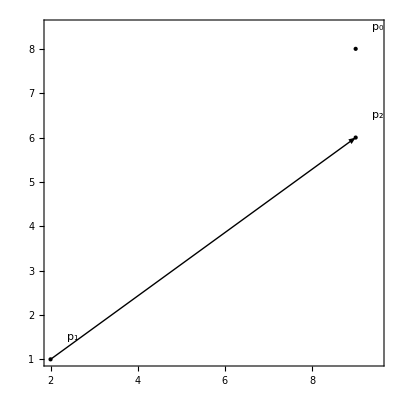

```mathematica
Subscript[x, 1]=RandomChoice[Range[10]];Subscript[y, 1]=RandomChoice[Range[10]];Subscript[x, 2]=RandomChoice[Range[10]];Subscript[y, 2]=RandomChoice[Range[10]];Subscript[x, 0]=RandomChoice[Range[10]];Subscript[y, 0]=RandomChoice[Range[10]];
Subscript[p, 1]={Subscript[x, 1],Subscript[y, 1]};
Subscript[p, 2]={Subscript[x, 2],Subscript[y, 2]};
Subscript[p, 0]={Subscript[x, 0],Subscript[y, 0]};
d=Det[({{Subscript[x, 0]-Subscript[x, 1], Subscript[y, 0]-Subscript[y, 1]}, {Subscript[x, 2]-Subscript[x, 1], Subscript[y, 2]-Subscript[y, 1]}})];
If[d>0,"Правее",If[d==0, "На прямой", "Левее"]]
Show[Graphics[{Thick,Black,Arrow[{Subscript[p, 1],Subscript[p, 2]}],Text["p_1",{Subscript[x, 1]+0.5,Subscript[y, 1]+0.5}],Text["p_2",{Subscript[x, 2]+0.5,Subscript[y, 2]+0.5}],Text["p_0",{Subscript[x, 0]+0.5,Subscript[y, 0]+0.5}],PlotLabel->info,Point[{Subscript[x, 1],Subscript[y, 1]}],Point[{Subscript[x, 2],Subscript[y, 2]}],Point[{Subscript[x, 0],Subscript[y, 0]}]},PlotRange->{{15,-5},{15,-5}},Frame->True]]
```

Задача 2

Дано: Точки p_1(x_1, y_1), p_2(x_2, y_2), p_3(x_3, y_3), p_4(x_4, y_4);

Надо: Определить пересекаются ли отрезки p_1 p_2 и p_3 p_4?

Примечания: в качестве результата выдается сообщение о положении
отрезков и картинка с изображением отрезков.

Решение:

Не пересекаются

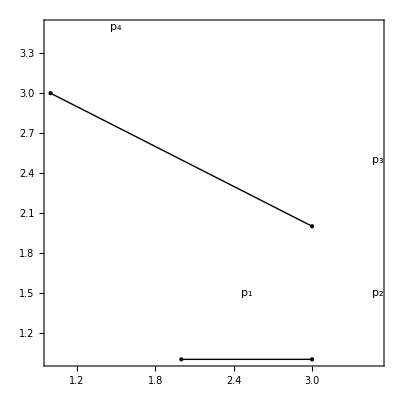

```mathematica
n=3;
Subscript[x, 1]=RandomChoice[Range[n]];Subscript[y, 1]=RandomChoice[Range[n]];Subscript[x, 2]=RandomChoice[Range[n]];Subscript[y, 2]=RandomChoice[Range[n]];Subscript[x, 3]=RandomChoice[Range[n]];Subscript[y, 3]=RandomChoice[Range[n]];
Subscript[x, 4]=RandomChoice[Range[n]];
Subscript[y, 4]=RandomChoice[Range[n]];
(*
Subscript[x, 1]=1;
Subscript[y, 1]=1;
Subscript[x, 2]=2;
Subscript[y, 2]=2;
Subscript[x, 3]=3;
Subscript[y, 3]=3;
Subscript[x, 4]=4;
Subscript[y, 4]=4;
*)
Subscript[p, 1]={Subscript[x, 1],Subscript[y, 1]};
Subscript[p, 2]={Subscript[x, 2],Subscript[y, 2]};
Subscript[p, 3]={Subscript[x, 3],Subscript[y, 3]};
Subscript[p, 4]={Subscript[x, 4],Subscript[y, 4]};
Subscript[d, 1]=Det[({{Subscript[x, 1]-Subscript[x, 3], Subscript[y, 1]-Subscript[y, 3]}, {Subscript[x, 4]-Subscript[x, 3], Subscript[y, 4]-Subscript[y, 3]}})];
Subscript[d, 2]=Det[({{Subscript[x, 2]-Subscript[x, 3], Subscript[y, 2]-Subscript[y, 3]}, {Subscript[x, 4]-Subscript[x, 3], Subscript[y, 4]-Subscript[y, 3]}})];
Subscript[d, 3]=Det[({{Subscript[x, 3]-Subscript[x, 1], Subscript[y, 3]-Subscript[y, 1]}, {Subscript[x, 2]-Subscript[x, 1], Subscript[y, 2]-Subscript[y, 1]}})];
Subscript[d, 4]=Det[({{Subscript[x, 4]-Subscript[x, 1], Subscript[y, 4]-Subscript[y, 1]}, {Subscript[x, 2]-Subscript[x, 1], Subscript[y, 2]-Subscript[y, 1]}})];
Subscript[v, 1]=(Subscript[p, 1]-Subscript[p, 3]).(Subscript[p, 1]-Subscript[p, 4]);
Subscript[v, 2]=(Subscript[p, 2]-Subscript[p, 3]).(Subscript[p, 2]-Subscript[p, 4]);
Subscript[v, 3]=(Subscript[p, 3]-Subscript[p, 1]).(Subscript[p, 3]-Subscript[p, 2]);
Subscript[v, 4]=(Subscript[p, 4]-Subscript[p, 1]).(Subscript[p, 4]-Subscript[p, 2]);
(*
(x-Subscript[x, 1])/(Subscript[x, 2]-Subscript[x, 1])=(y-Subscript[y, 1])/(Subscript[y, 2]-Subscript[y, 1]);
(x-Subscript[x, 3])/(Subscript[x, 4]-Subscript[x, 3])=(y-Subscript[y, 3])/(Subscript[y, 4]-Subscript[y, 3]);
*)
(*
xx=(Subscript[x, 1]*Subscript[y, 2]-Subscript[x, 2]*Subscript[y, 1])*(Subscript[x, 4]-Subscript[x, 3])-(Subscript[x, 3]*Subscript[y, 4]-x4*y3)*(x2-x1))/((y1-y2)*(x4-x3)-(y3-y4)*(x2-x1));
y:=((y3-y4)*x-(x3*y4-x4*y3))/(x4-x3);
*)
(*
xx=((Subscript[x, 1]*Subscript[y, 2]-Subscript[x, 2]*Subscript[y, 1])*(Subscript[x, 4]-Subscript[x, 3])-(Subscript[x, 3]*Subscript[y, 4]-Subscript[x, 4]*Subscript[y, 3])*(Subscript[x, 2]-Subscript[x, 1]))/((Subscript[y, 1]-Subscript[y, 2])*(Subscript[x, 4]-Subscript[x, 3])-(Subscript[y, 3]-Subscript[y, 4])*(Subscript[x, 2]-Subscript[x, 1]));
yy=((Subscript[y, 3]-Subscript[y, 4])*x-(Subscript[x, 3]*Subscript[y, 4]-Subscript[x, 4]*Subscript[y, 3]))/(Subscript[x, 4]-Subscript[x, 3]);
*)
(*
If[(((Subscript[x, 1]≤xx)&&(Subscript[x, 2]≥xx)&&(Subscript[x, 3]≤xx)&&(Subscript[x, 4]≥xx))||((Subscript[y, 1]≤yy)&&(Subscript[y, 2]≥yy)&&(Subscript[y, 3]≤yy)&&(Subscript[y, 4]≥yy))),"Пересекаются","Не пересекаются"]
*)
If[Subscript[d, 1]==0&&Subscript[d, 2]==0&&Subscript[d, 3]==0&&Subscript[d, 4]==0,{If[Subscript[p, 1]==Subscript[p, 2]&&Subscript[p, 3]==Subscript[p, 4],{"Отрезки являются точками",If[Subscript[p, 1]==Subscript[p, 3],"Совпадают","Не совпадают"]},{"Лежат на одной прямой",If[Subscript[v, 1]≤0||Subscript[v, 2]≤0||Subscript[v, 3]≤0||Subscript[v, 4]≤0,"Пересекаются","Не пересекаются"]}]},
If[Subscript[d, 1]*Subscript[d, 2]≤0&&Subscript[d, 3]*Subscript[d, 4]≤0,"Пересекаются","Не пересекаются"]
]
Show[Graphics[{Thick,Black,Line[{Subscript[p, 1],Subscript[p, 2]}],Line[{Subscript[p, 3],Subscript[p, 4]}],Text["p_1",{Subscript[x, 1]+0.5,Subscript[y, 1]+0.5}],Text["p_2",{Subscript[x, 2]+0.5,Subscript[y, 2]+0.5}],Text["p_3",{Subscript[x, 3]+0.5,Subscript[y, 3]+0.5}],Text["p_4",{Subscript[x, 4]+0.5,Subscript[y, 4]+0.5}],PlotLabel->info,Point[{Subscript[x, 1],Subscript[y, 1]}],Point[{Subscript[x, 2],Subscript[y, 2]}],Point[{Subscript[x, 3],Subscript[y, 3]}],Point[{Subscript[x, 4],Subscript[y, 4]}]},PlotRange->{{10,-5},{10,-5}},Frame->True]]
```

Задача 3

Дано: P = {p_1(x_1, y_1), p_2(x_2, y_2), … ,p_n(x_n, y_n)};

Надо: Определить, является ли многоугольник P простым многоугольником?

Примечания: в качестве результата выдается сообщение и картинка с изображением многоугольника с подписанными вершинами.

Решение:

7

{{6,7},{3,1},{7,6},{3,5},{6,8},{9,5},{1,7}}

Не простой

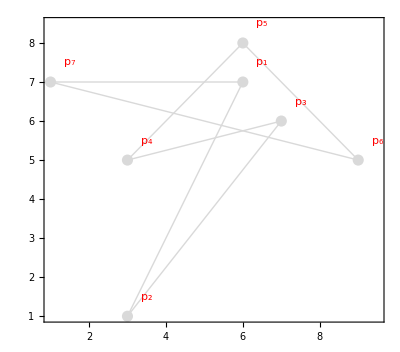

```mathematica
n=RandomChoice[Range[3,10]]
Do[{Subscript[x, k]=RandomChoice[Range[10]],Subscript[y, k]=RandomChoice[Range[10]],Subscript[p, k]={Subscript[x, k],Subscript[y, k]}},{k,1,n}];
Table[Subscript[p, k],{k,1,n}]
isSimple=True;
For[i=1,i+2≤n,i++,
For[j=i+2,j≤n&&j-i≤n-2,j++,
If[Det[({{Subscript[x, i]-Subscript[x, j], Subscript[y, i]-Subscript[y, j]}, {Subscript[x, Mod[j,n]+1]-Subscript[x, j], Subscript[y, Mod[j,n]+1]-Subscript[y, j]}})]*Det[({{Subscript[x, i+1]-Subscript[x, j], Subscript[y, i+1]-Subscript[y, j]}, {Subscript[x, Mod[j,n]+1]-Subscript[x, j], Subscript[y, Mod[j,n]+1]-Subscript[y, j]}})]≤0&&Det[({{Subscript[x, j]-Subscript[x, i], Subscript[y, j]-Subscript[y, i]}, {Subscript[x, i+1]-Subscript[x, i], Subscript[y, i+1]-Subscript[y, i]}})]*Det[({{Subscript[x, Mod[j,n]+1]-Subscript[x, i], Subscript[y, Mod[j,n]+1]-Subscript[y, i]}, {Subscript[x, i+1]-Subscript[x, i], Subscript[y, i+1]-Subscript[y, i]}})]≤0,{isSimple=False,Break[]},]
];
If[isSimple==False,Break[]]
];
If[isSimple==True,"Простой","Не простой"]
Show[Graphics[{PointSize[0.02],Thick,LightGray,Table[Line[{Subscript[p, k],Subscript[p, Mod[k,n]+1]}],{k,1,n}],Table[Text[Style[Subscript["p", k],Red],{Subscript[x, k]+0.5,Subscript[y, k]+0.5}],{k,1,n}],PlotLabel->info,Point[Table[Subscript[p, k],{k,1,n}]]},PlotRange->{{15,-5},{15,-5}},Frame->True]]
```